```mathematica
Subscript[rho, crit] = 1.5*10^-7; 
f = 0.1;
p = 1.9;
c= 10;
G = 0.0045;
k = 2;
Mprimary = 10^12;
m22 = 1;
ksol = 9.1*10^-2;
cuttoff = 5 10^8;
```

```mathematica
MaxRadius[M_]:=  (3 M/(4 Pi *200 * Subscript[rho, crit]))^(1/3)
SolitonMass[M_]:=2.7 * 10^8 /m22 * (M/10^10)^(1/3)
HalfSolitonRadius[M_]:= 33 Pi^2/(1024 ksol^(3/2)) 1.9*10^10/(SolitonMass[M]) m22 ^ -2
SolitonProfile[r_, M_]:=Module[{Msol = SolitonMass[M],R12 = HalfSolitonRadius[M]},  (1.9*10^10) m22^-2 *(1/R12)^4/(1+ksol (r/R12)^2)^8]
NFWProfile[r_,M_]:= Module[{Rmax =MaxRadius[M]},Module[{ Rc = Rmax / c}, 200/3 Subscript[rho, crit]/(Log[1+c] - c/(1+c))c^3If[r < Rmax, 1/(r/Rc*(1+r/Rc)^2), 0]]]
Subscript[MFree, nfw][r_, M_] := Module[{Rmax = MaxRadius[M]},Module[{ Rc = Rmax / c}, M*If[r < Rmax, (Log[1+r/Rc]-r/(r+Rc))/(Log[1+c] - c/(1+c)), 1]]]
RhoFree[r_, M_] := Module[{R12 = HalfSolitonRadius[M]},If[r < MaxRadius[M], If[r<R12, SolitonProfile[r, M] + NFWProfile[R12, M], SolitonProfile[r, M] + NFWProfile[r, M]], 0]]

SolitonMassProfile[r_, M_]:= Module[{Msol = SolitonMass[M],R = HalfSolitonRadius[M]/Sqrt[ksol]},  Msol ArcTan[r/R]/(Pi/2)+ Msol/(3465 Pi/2(R^2+r^2)^7)*(3465 R r^13 +23100 R^3 r^11 + 65373 R^5 r^9 + 101376 R^7 r^7 + 92323 R^9 r^5 + 48580 R^11 r^3 - 3465 R^13 r)]

MFree[r_, M_]:= Module[{R12 = HalfSolitonRadius[M], Rmax = MaxRadius[M]}, If[r< Rmax, SolitonMassProfile[r, M], SolitonMassProfile[Rmax,M]] + If[r < R12,4/3Pi r^3 NFWProfile[R12, M] , Subscript[MFree, nfw][r,M]- Subscript[MFree, nfw][R12, M] +4/3Pi R12^3 NFWProfile[R12, M]]]

Subscript[PhiFree, nfw][r_, M_] :=Module[{Rmax = MaxRadius[M]},Module[{ Rc = Rmax / c}, -M*G/Rmax*If[r < Rmax, (Rmax/r * Log[1+r/Rc]-Log[1+c])/(Log[1+c]-c/(1+c)) + 1, Rmax/r]]]


Subscript[N, halo][M_, R_] := M^-p  *NFWProfile[R, Mprimary]  * (2-p) f^(p-1) Mprimary^(p-2)

TidalRadius[m_,R_]:= R*(m/(2*Subscript[MFree, nfw][R,Mprimary]))^(1/3)
Truncate[m_, R_]:= Subscript[MFree, nfw][TidalRadius[m,R],m]

MSubHalo[r_, M_, R_] := Module[{Rt = TidalRadius[M,R]}, If[r < Rt, MFree[r, M], MFree[Rt, M]]]

PotChange[m_,R_,r_]:=If[r> 0, MSubHalo[r, m, R] *G/r^2, 0]
```

```mathematica
TidalLimit[M_]:= Module[{Msol = SolitonMass[M],R = HalfSolitonRadius[M]/Sqrt[ksol]},  -2Msol G/R^3 (48580/3465 - 1/3 + 7) 2/Pi  + 4/3 Pi NFWProfile[R Sqrt[ksol], M] 2 G- 4Pi G RhoFree[0, M]]
```

```mathematica
SubHaloTidalForce[r_, m_, D_]:= Module[{Rt = TidalRadius[m, D]},If[r < 10^-2, TidalLimit[m], 2 G MSubHalo[r,m, D]/r^3 - 4 Pi G If[r < Rt, RhoFree[r, m],0]]]
```

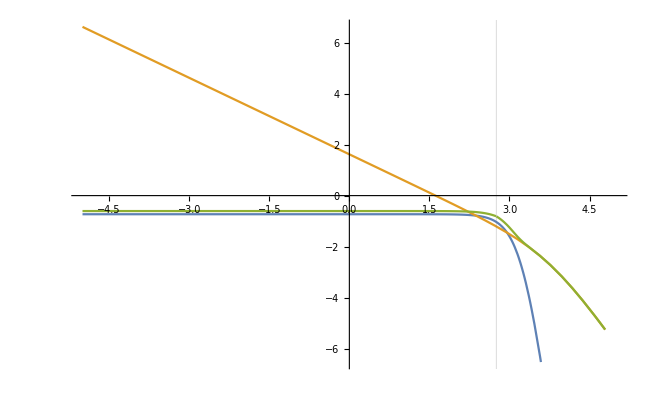

```mathematica
Mtest = 3 10^10;
Plot[{Log10[SolitonProfile[10^x,Mtest]], Log10[NFWProfile[10^x, Mtest]],Log10[RhoFree[10^x,Mtest]]}, {x,-5, 5}, GridLines->{{Log10[HalfSolitonRadius[Mtest]]}, {0,0,0}}]
```

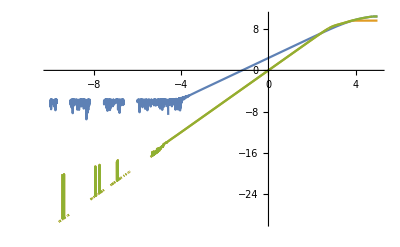

```mathematica
Plot[{ Log10[Subscript[MFree, nfw][10^r, Mtest]], Log10[MSubHalo[10^r, Mtest, 10^4]], Log10[MFree[10^r, Mtest]]},{r,-10,5}]
```

```mathematica
Mreal[Mvir_]:= Mvir - Subscript[MFree, nfw][HalfSolitonRadius[Mvir], Mvir] + 4/3Pi HalfSolitonRadius[Mvir]^3 NFWProfile[HalfSolitonRadius[Mvir], Mvir] +SolitonMass[Mvir]
```

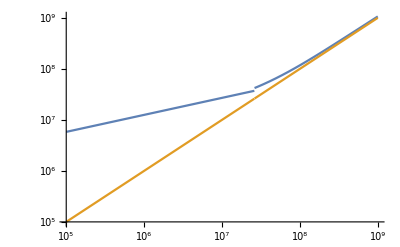

```mathematica
LogLogPlot[{Mreal[Mvir], Mvir}, {Mvir,  10^5, 10^9}]
```

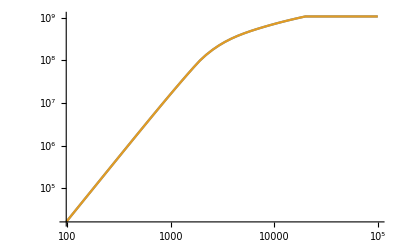

```mathematica
LogLogPlot[{MFree[r, 10^9], NIntegrate[4Pi x^2 RhoFree[x, 10^9], {x, 0, r}]}, {r, 0, 10^5}]
```

```mathematica
Limit[2 MFree[r, 3]/r^3, r->0]
```

0.

```mathematica
SubHaloTidalForce[r_, m_, D_]:=  Module[{Rmax = Min[TidalRadius[m,D], MaxRadius[m]]},Module[{ Rc = MaxRadius[m]/ c}, (k-1)*m G*If[r < 10^-1, 2/(3 Rc^3)/(Log[1+c] - c/(1+c)), 1/r^3 If[r < Rmax, (2Log[1+r/Rc]-r(3r+2Rc)/(r+Rc)^2)/(Log[1+c] - c/(1+c)), 2 Truncate[m, D]/m]]]]
```

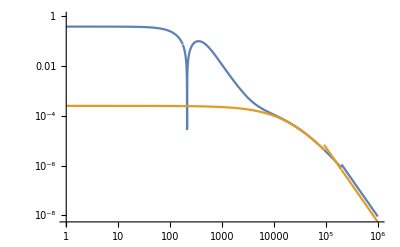

```mathematica
LogLogPlot[{Abs[-2 G MFree[r, 10^12]/r^3 + 4 Pi G RhoFree[r, 10^12]], SubHaloTidalForce[r, 10^12, 10^5]}, {r, 1, 10^6}]
```

```mathematica
Fluc[D_]:=NIntegrate[4Pi  R^2  * Subscript[N, halo][m, D]*(PotChange[m,D,R])^2 * (-Subscript[PhiFree, nfw][D, Mprimary]/3),{R, 0, D/2},{m, cuttoff, f Mprimary}]
```

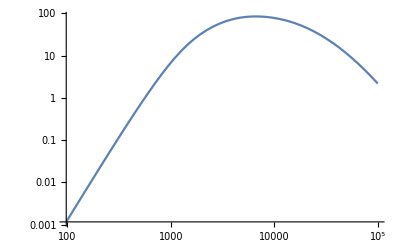

```mathematica
LogLogPlot[Fluc[x], {x, 0 ,10^5}]
```

```mathematica
NatrualNormalize[R_]:= (Subscript[PhiFree, nfw][R, Mprimary])^2* 4Pi Subscript[MFree, nfw][R, Mprimary]/R^3;
NormedFluc[D_]:= Fluc[D]/NatrualNormalize[D];
```

```mathematica
NormedFluc[D_]:= Fluc[D]/NatrualNormalize[D];
```

```mathematica
TidalVariance[D_]:= NIntegrate[4Pi R^2  Subscript[N, halo][m, D] (SubHaloTidalForce[R, m, D])^2, {R, 0.2, D/2},{m, 1, f Mprimary}]/(2 Subscript[MFree, nfw][D, Mprimary] G / D^3 - 4 Pi Subscript[RhoFree, nfw][D, Mprimary] G)^2
```

```mathematica
logtidaltab = Quiet[Table[{n/5, Log10[TidalVariance[10^(n/5)]]}, {n, 0, 40}]];
tidaltab = Quiet[Table[{n, Sqrt[TidalVariance[10^3n]]}, {n, 1, 100}]];
ListPlot[logtidaltab,  AxesLabel->{"log(r/pc)","log(Var(F))"}, LabelStyle->Directive[Black, Medium], Joined->True]
ListPlot[tidaltab,  AxesLabel->{"r(kpc)","σ_F"}, LabelStyle->Directive[Black, Medium], Joined->True]
```

$Aborted

-Graphics-

ListPlot::lpn: tidaltab is not a list of numbers or pairs of numbers.

General::stop: Further output of ListPlot::lpn will be suppressed during this calculation.

ListPlot[tidaltab,AxesLabel→{r(kpc),σ_F},LabelStyle→Directive[GrayLevel[0],Medium],Joined→True]